```mathematica
(**This code extends the vibration analysis of a rotating tapered Timoshenko Beam using finite beam element method
 outlined in the paper 
"A.Bazoune and Y.A.Khulief,“A finite beam element for vibration analysis of rotating tapered timoshenko beams,” J.Sound Vib.,vol.156,no.1,pp.141–164,1992,doi:10.1016/0022-460X(92)90817-H." to 3D beam element
The method is outlined in
Di.Zhou,J.Fang,H.Wang,and X.Zhang,“Three-Dimensional Dynamics Analysis of Rotating Functionally Gradient Beams Based on Timoshenko Beam Theory,” Int.J.Appl.Mech.,vol.11,no.4,2019,doi:10.1142/S1758825119500406.
**)
(* The stiffnes matrices are unusually complex, So numerical method is resorted..This code generates matrices numerically and calculates the natural frequencies using eigen value method.
There is option to select either Euler or Timoshenko theory for the beam
One can also choose to include or exclude the coriolois effect.
Sample results are also generate dat the end
*)
```

```mathematica
(**shape functions**)

(***This function calculates the 4th order shape function as mentioned in the paper for an Beam**)

Clear[ComputeShapeN,Φ];

ComputeShapeN[li_,{Φy_,Φz_}]:=Module[{ζ,av,disp},

ζ[xi_]:=xi/li;

Nu1[xi_]:= (1-ζ[xi]);Nu2[xi_]:=0;Nu3[xi_]:=ζ[xi];Nu4[xi_]:= 0;

Nv1[xi_]:= (1-3 ζ[xi]^2+2 ζ[xi]^3+Φz (1-ζ[xi]))/(1+Φz);

Nv2[xi_]:=  li (ζ[xi]-2 ζ[xi]^2+ζ[xi]^3+(ζ[xi]-ζ[xi]^2) Φz/2) /(1+Φz);

Nv3[xi_]:= (3 ζ[xi]^2-2 ζ[xi]^3+Φz ζ[xi])/(1+Φz);

Nv4[xi_]:= li (-ζ[xi]^2 +ζ[xi]^3+ (-ζ[xi]+ζ[xi]^2) Φz/2)/(1+Φz);

Nθz1[xi_]:= 6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φz));

Nθz2[xi_]:= (1-4 ζ[xi]+3 ζ[xi]^2+Φz (1-ζ[xi]))/(1+Φz);

Nθz3[xi_]:=-6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φz));

Nθz4[xi_]:= (-2 ζ[xi]+3 ζ[xi]^2+Φz ζ[xi])/(1+Φz);

Nw1[xi_]:=(1-3 ζ[xi]^2+2 ζ[xi]^3+(1-ζ[xi]) Φy)/(1+Φy);

Nw2[xi_]:=-(ζ[xi]-2 ζ[xi]^2+ζ[xi]^3+(ζ[xi]-ζ[xi]^2) Φy/2) li/(1+Φy);

Nw3[xi_]:=(3 ζ[xi]^2 - 2 ζ[xi]^3+ζ[xi] Φy)/(1+Φy);

Nw4[xi_]:=-(-ζ[xi]^2+ζ[xi]^3-(ζ[xi]-ζ[xi]^2) Φy/2) li/(1+Φy);

Nθy1[xi_]:=6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φy));

Nθy2[xi_]:= -(1-4 ζ[xi]+3 ζ[xi]^2+Φy (1-ζ[xi]))/(1+Φy);

Nθy3[xi_]:=-6 (-ζ[xi]+ζ[xi]^2)/(li (1+Φy));

Nθy4[xi_]:= -(-2 ζ[xi]+3 ζ[xi]^2+Φy ζ[xi])/(1+Φy);

Nθx1[xi_]:=0;Nθx2[xi_]:=(1-ζ[xi]);Nθx3[xi_]:=0;Nθx4[xi_]:=ζ[xi];

(**shape function matrices***)

(**displacements shape functins *)(**12 x 12 matrix*)

(*vectors*)

av={u1,θx1,u2,θx2};b1v={v1,θz1,v2,θz2};b2v={w1,θy1,w2,θy2};

(*glolbal vector*)

egi=Flatten@Transpose@{{u1,θx1,u2,θx2},{v1,θy1,v2,θy2},{w1,θz1,w2,θz2}};

Nu[xi_]={Coefficient[#.av,egi]&@{Nu1[xi],Nu2[xi],Nu3[xi],Nu4[xi]}};

Nv[xi_]={Coefficient[#.b1v,egi]&@{Nv1[xi],Nv2[xi],Nv3[xi],Nv4[xi]}};

Nw[xi_]={Coefficient[#.b2v,egi]&@{Nw1[xi],Nw2[xi],Nw3[xi],Nw4[xi]}};

(**shear deformation shape functions *)

Nθx[xi_]={Coefficient[#.av,egi]&@{Nθx1[xi],Nθx2[xi],Nθx3[xi],Nθx4[xi]}};

Nθy[xi_]={Coefficient[#.b2v,egi]&@{Nθy1[xi],Nθy2[xi],Nθy3[xi],Nθy4[xi]}};

Nθz[xi_]={Coefficient[#.b1v,egi]&@{Nθz1[xi],Nθz2[xi],Nθz3[xi],Nθz4[xi]}};

(**shape function matrix for cooriolois component*)

(***derivation of Shape function matrix**)

Clear[u,v,w,θx,θy,θz];

disp={Ui,Vi,Wi}->{u[xi]-yi v'[xi]-zi w'[xi],-zi θx[xi]+v[xi],yi θx[xi]+w[xi]};

ClearAll[u,v,w,θx,θy,θz];

{u[xi_]=Nu[xi].egi,v[xi_]=Nv[xi].egi,w[xi_]=Nw[xi].egi,

θx[xi_]=Nθx[xi].egi,θy[xi_]=Nθy[xi].egi,θz[xi_]=Nθz[xi].egi};

(**display Si matrix**)

Si[xi_,y_,zi_]=ParallelMap[Simplify,(Coefficient[#,egi]&/@Flatten[({Ui,Vi,Wi}/.disp)])];

ClearAll[u,v,w,θx,θy,θz];

];

(*

ComputeShapeN[li,{Φy,Φz}];*)

(***rotational transformation matrices**)

delta:=10^-15;

Clear[Ri];

clengths={cx->(x2-x1)/li,cy->(y2-y1)/li,cz->(z2-z1)/li};

rot=Ri->{{cx,-cx cy/Norm[{cx,cz}],-cz/Norm[{cx,cz}]},{cy,Norm[{cx,cz}],0},{cz,-cx cy/Norm[{cx,cz}],cx /Norm[{cx,cz}]}}/.clengths;

val={x2->x1+li,y2->y1,z2->z1};

Ribar=ArrayFlatten@(DiagonalMatrix[{Ri,Ri,Ri,Ri}]/.rot)/.val;

Ri=Ri/.rot/.val;

(**get coriolois matrix form file*)

DumpGet[NotebookDirectory[]<>"Coriolois.mx"]

CTa[li,xi,b,h,ρ,Φy,Φz,ψ]//Variables
```

{b,h,li,xi,ρ,Φy,Φz,Cos[ψ],Sin[ψ],Sin[2 ψ]}

```mathematica
(**basic geometric paramters derived calcuations form minimum set of given variables*)

ClearAll[gparam];

gparam[gp_]:=Module[{sol,sol1},

vars={b0,h0,ay,az,A0,I0yy,I0zz,L};

nvar=#[[1]]&/@gp;

uvars=Complement[vars,nvar];

sol=Solve[{I0yy==b0 h0^3/12,I0zz==b0^3 h0/12,A0==b0 h0,ay==Sqrt[I0yy/A0]/L,az==Sqrt[I0zz/A0]/L}/.gp,uvars];

(**select positive*)

Table[e=sol[[i]];If[And@@Thread[(uvars/.e)>0],sol1=e;];,{i,1,Length[sol]}];

sol1//Return;]

(**generatioon of geom paramters*)

ClearAll[GenGeomParameters];

(*options argument is optional, default it will evaluate numerically except when {Symbolic->True}is passed for use in printing matrices*)

GenGeomParameters[νy_,νz_,gp_,L_,n_,ψ_,options_:{Symbolic->False}]:=Module[{},

pr={νy1->νy,νz1->νz};

(***basic paramters in terms of element no i and (L, n->nelement)***)

lengths0={L0y->L/νy1,L0z->L/νz1,li->L/n};

lengths1={Liy->L0y-Li,Liz->L0z-Li}/.Li->(i-1)li;

(*definition of variables for matrices*)

mus={μ1->Liy Liz,μ2->(Liy+Liz)/2}/.lengths1/.lengths0;

alphas={αy0->μ1 Liy^2,αy1->Liy^3+3μ1 Liy,αy2->6 μ2 Liy,αy3->2 (Liy+μ2),αz0->μ1 Liz^2,αz1->Liz^3+3μ1 Liz,αz2->6 μ2 Liz,αz3->2 (Liz+μ2)}/.mus/.lengths1/.lengths0;

betas={β0->1/2 μ1 li^2(n^2-i^2+2i-1)-2/3μ2 li^3(n^3-i^3+3/2 i-1/2)+1/4 li^4(n^4-i^4+4/3 i-1/3),β1->μ1 Li,

β2->1/2(μ1-2μ2 Li),β3->1/3(Li-2μ2),β4->1/4}/.Li->(i-1)li/.mus/.lengths1/.lengths0;

gammas={Γyy->I0yy/L0y/L0z^3,Γzz->I0zz/L0z/L0y^3}/.lengths1/.lengths0;

(**basic geom params*)

r2=Union[gp,gparam[gp]];

(**slenderness ratio ay=(rgy/L) az=(rgz/L*)

(*r2y={I0yy->A0 ay^2 L^2};

r2z={I0zz->A0 az^2 L^2};

r2=Union[r2y,r2z];*)

Clear[A,Iyy,Izz,J,Iy1y1,Iy1z1,Iyz,Iz1z1];

A[xi_]=((A0/(L0y L0z)) (μ1 -2 μ2 xi+xi^2)/.mus/.lengths0//Simplify)/.pr//Simplify;

Iy1y1[xi_]=(Γyy*(αz0-αz1 xi+αz2 xi^2-αz3 xi^3+xi^4)/.gammas/.alphas/.lengths0/.r2//Simplify)/.pr//Simplify;

Iz1z1[xi_]=(Γzz*(αy0-αy1 xi+αy2 xi^2-αy3 xi^3+xi^4)/.gammas/.alphas/.lengths0/.r2//Simplify)/.pr//Simplify;

Iy1z1[xi_]=0;

(***moments with coordinate transformation**)

Iyy[xi_]:=Iy1y1[xi] Cos[ψ]^2+Iz1z1[xi] Sin[ψ]^2-Iy1z1[xi] Sin[2 ψ];

Iyz[xi_]:=(Iy1y1[xi] -Iz1z1[xi] )Sin[ψ] Cos[ψ]+Iy1z1[xi] Cos[2 ψ];

Izz[xi_]:=Iy1y1[xi] Sin[ψ]^2+Iz1z1[xi] Cos[ψ]^2+Iy1z1[xi] Sin[2 ψ];

J[xi_]:=Iy1y1[xi]+Iz1z1[xi];

];

(***This module calculates phi value for ith element of the beam

as a function of element number i and xi * this is required for boundary function of Timoshenko beam theory***)

ClearAll[Phi];(*Beamtype can be supplied with "Timo"  for Timoshenko, "Euler" for Euler*) 

(***requires definition of {pr,lengths0,lengths1,mus,betas,alphas,r2} to execute properly*)

Phi[xi_,{ky_,kz_}, μ_, BeamType_:"Timo",options_:{Symbolic->False}]:=

Module[{phi},

(*poisson relation*)pois=Gi->Ei/(2 (1+μ));

(**phi*)

Switch[BeamType,"Timo",

phi={Φz->12 Ei Izz[xi]/(ky Gi A[xi] li^2),Φy->12 Ei Iyy[xi]/(kz Gi A[xi] li^2)};

If[(Symbolic/.options)==False,phi=(phi/.r2/.pois/.lengths0/.mus/.alphas//Simplify)/.pr//Simplify;],

"Euler",phi={Φy->0,Φz->0};];

Return[phi]

]
```

```mathematica
(**mod**)

CalcMat[{ψ_,ϕ_},gp_, {ky_,kz_}, μ_, νy_, νz_,n1_,L1_,R0_,TheoryType_:"Timo"]:=

Module[{L=L1,s1,s2,s3,s4,s5,s6,s7,s9,gs,rx},

ClearAll[Meebar,Mtwbar,CTi1,Keebar,𝕜c];

(***basic paramters in terms of element no i and (L, n->nelement)***)

lengths0={L0y->L/νy1,L0z->L/νz1,li->L/n};

lengths1={Liy->L0y-Li,Liz->L0z-Li}/.Li->(i-1)li;

(**generates different matrices**)

(***stiffness matrices**)

(** phis shear paramters*)

GenGeomParameters[νy,νz,gp,L,n,ψ];

phis[i_,xi_]=Phi[xi,{ky,kz}, μ,TheoryType]/.xi->(Li+li)/2/.Li->(i-1)li/.lengths0;

ComputeShapeN[li,{Φy,Φz}];

pr={νy1->νy,νz1->νz,n->n1};

(*characterics scales for nondimensionalization*)

nd0={(**characteristic stiffness*)

K0->Ei I0yy/L^3,

(**charecteristic mass*)

M0->ρ A0 L};

(*speed*)

nd1={Ω0->Sqrt[K0/M0]};

(*comb*)

nd=Union[nd0,nd1/.nd0];

(***********************)

(***Elemental stiffness matrices****)

(***axial stiffness**)

s1=Ka->Ei A[xi] Transpose[Nu'[xi]].Nu'[xi];

(***bending stiffness in xz**)

s2=Kbv-> Ei Izz[xi] Transpose[Nθz'[xi]].Nθz'[xi];

(***bending stiffness in xy**)

s3=Kbw->Ei Iyy[xi] Transpose[Nθy'[xi]].Nθy'[xi];

(***torsioonal stiffness in z**)

s4=Kθx->Gi J[xi] Transpose[Nθx'[xi]].Nθx'[xi];

(**bending stiffness coiupling*)

s5=Kbvw->Ei Iyz[xi]Transpose[Nθy'[xi] Nθz'[xi]].(Nθy'[xi]Nθz'[xi]);

(*elemental shear stiffness in xy plane**)

s6=Ksv->ky Gi A[xi]Transpose[Nv'[xi]-Nθz[xi]]. (Nv'[xi]-Nθz[xi]);

s7=Ksw->kz Gi A[xi](Transpose[Nw'[xi]-Nθy[xi]]. (Nw'[xi]-Nθy[xi]));

(*Centrifugal force*)

rf=Fp->ρ Ω^2 (Integrate[(R0+((i-1)li+xi)Cos[ϕ])A[xi],{xi,xi,li}]+Integrate[(R0+xi Cos[ϕ])A[xi],{xi,i li,n li}]);

(**stiffness matrix due to rotation*)

s8=Kcv->(Transpose[Nv'[xi]].Nv'[xi])Fp/.rf;

s9=Kcw->(Transpose[Nw'[xi]].Nw'[xi])Fp/.rf;

(**combined stiffness*)

gs={s1,s2,s3,s4,s5,s6,s7,s8,s9};

Switch[TheoryType,"Timo",comp={Kee->Ka+Kbv+Kbw+Kbvw+Kθx+Ksv+Ksw,Kc->Kcv+Kcw};,

"Euler",

(*Euler*)

comp={Kee->Ka+Kbv+Kbw+Kbvw+Kθx,Kc->Kcv+Kcw};

];

(*****definition ***)

Keebar[i_,ξ_]=Module[{k11},

k11=(ParallelMap[Simplify[Chop[#]]&,li*(Kee/K0)/.nd/.comp/.gs/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0]);

k11=ParallelMap[Simplify[Chop[#]]&,(k11)/.pr];

k11

];

𝕜c[i1_,ξ_]=Module[{Kcds1},

Kcds1=((li*Kc/Ω^2)/M0)/.nd/.comp/.gs/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0;

Simplify[Kcds1]/.pr/.i->i1//Simplify

];

(***********************)

(**mass matrices**)

massms:={ma->Transpose[Nu[xi]].Nu[xi] ρ A[xi],

mθx->Transpose[Nθx[xi]].Nθx[xi] ρ J[xi],

mtv->Transpose[Nv[xi]].Nv[xi] ρ A[xi],

mtw->Transpose[Nw[xi]].Nw[xi] ρ A[xi],

mθzv->Transpose[Nθy[xi]].Nθy[xi] ρ Iyy[xi],

mθyw->Transpose[Nθz[xi]].Nθz[xi] ρ Iyy[xi],

mθvw->Transpose[Nθy[xi]].Nθz[xi] ρ Iyz[xi]};

(**elastic*)

Switch[TheoryType,"Timo",

Meebar[i_,ξ_]=Module[{mee1},

mee1=Plus@@{ma,mθx,mtv,mtw,mθzv,mθyw,mθvw}/.massms;

mee1=li (mee1/M0)/.nd/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0;

ParallelMap[Simplify[Chop[#]]&,mee1]/.pr//Simplify

];,"Euler",

Meebar[i_,ξ_]=Module[{mee1},

mee1=Plus@@{ma,mθx,mtv,mtw}/.massms;

mee1=li (mee1/M0)/.nd/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0;

ParallelMap[Simplify[Chop[#]]&,mee1]/.pr//Simplify

];

];

(*translation mass matrix*)

Mtwbar[i_,ξ_]=Module[{mtw1},

mtw1=mtw/.massms;

mtw1=li (mtw1/M0)/.nd/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0;

ParallelMap[Simplify[#]&,mtw1]/.pr

];

ClearAll[bi,hi,CTi1];

(**c/s size for integration*)

bi[xi_]=b0*(1-(xi+(i-1)li)/L0y);

hi[xi_]=h0*(1-(xi+(i-1)li)/L0z);

(**coriolois matrix*)

CTi1[i_,ξ_]=Module[{ct1},

ct1=CTa[li,xi,bi[xi],hi[xi],ρ,Φy,Φz,ψ];

ct1=li (ct1/M0)/.nd/.phis[i,xi]/.r2/.pois/.mus/.xi->ξ li/.lengths0;

ct1=ParallelMap[Simplify@#&,ct1]/.pr;

ParallelMap[Simplify@#&,ct1]

];

]
```

```mathematica
(***module to numerically integrate***)

(**used the inbuilt NIntegrate module. gives accurate results.. the output may differ slightly in few insignificant digits due to more accuracy than that used in paper*)

SetOptions[NIntegrate,{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}];

ClearAll[Contribute];

Contribute[i1_?NumericQ]:=Module[{Mee,Mtw,CT,Kee,𝕜,ir},ir=i->i1;

{Mee,Mtw,CT,Kee,𝕜}={NIntegrate[Meebar[i,ξ]/.ir,{ξ,0,1},{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}],

NIntegrate[Mtwbar[i,ξ]/.ir,{ξ,0,1},{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}],

NIntegrate[CTi1[i,ξ]/.ir,{ξ,0,1},{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}],

NIntegrate[Keebar[i,ξ]/.ir,{ξ,0,1},{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}],

NIntegrate[𝕜c[i,ξ]/.ir,{ξ,0,1},{MinRecursion->4,AccuracyGoal->8,PrecisionGoal->8}]};

Return[{Mee,Mtw,CT,Kee,𝕜}];

]
```

```mathematica
(***********************************)

(***apply boundary conditions***) (**Timoshenko Beam theory**)

(*function for applying point bc specify type of beam theory by giving keyword "Euler" or "Timo"  default is "Timo" 

and boundary type any valid combination of clamped hinged or free. *)

(**boundary conditions used are

Clamped:displacement and angle =0 

hinged: displacement =0 bendining moment=0

Free end : shear force =0, bending moment =0*)

Clear[BCPoint];BCPoint[{u_,v_,w_,thx_,thy_,thz_},p_,type_,BeamType_:"Timo"]:=



Switch[BeamType,

"Euler",

Switch[type,

"Clamped",{u[p]==0,v[p]==0,w[p]==0,v'[p]==0,w'[p]==0,thx[0]==0},

"Hinged",{u[p]==0,v[p]==0,w[p]==0,thx[0]==0,v''[p]==0,w''[p]==0},

"Free",{v''[p]==0,0==w''[p],v'''[p]==0,w'''[p]==0}],

"Timo",

Switch[type,

"Clamped",{u[p]==0,v[p]==0,w[p]==0,thz[p]==0,thy[p]==0,thx[0]==0},

"Hinged",{u[p]==0,v[p]==0,w[p]==0,thx[p]==0,thz'[p]==0,thy'[p]==0},

"Free",{thy'[p]==0,thz'[p]==0,thz[p]-v'[p]==0,thy[p]-w'[p]==0}]

];

(***********************)

(*function for applying bc at both points of beam four type CF HF CH HH considered*)

Clear[BCBeam];BCBeam[v1_,v2_,type_,BeamType_:"Timo"]:=Module[{rep1,bclist,bc,typeb,bct},

rep1=Thread[{"C","F","H"}->{"Clamped","Free","Hinged"}];

bclist={};rep1=Thread[{"C","F","H"}->{"Clamped","Free","Hinged"}];

Table[bct=StringPartition[type,1]/.rep1;

AppendTo[bclist,type];

AppendTo[bclist,Union[BCPoint[v1,0,bct[[1]],BeamType],BCPoint[v2,li,bct[[2]],BeamType]]];,{typeb,{"CF","HF","CH","HH"}}];

bc=Apply[Switch]@PrependTo[bclist,type];

Return[bc];

];

(**********************************)

(**genrates bounary rules takes input as beam type and theorytype and definition of phi*)

ClearAll[GenerateBRule];

GenerateBRule[n_,L_,btype_,BeamType_:"Timo"]:=

Module[{qq,q1,qn,tmat,vlist,Vl,Vr,eqns,bcs,blist},

qq:={u[#],v[#],w[#],θx[#],θy[#],θz[#],u[#+1],v[#+1],w[#+1],θx[#+1],θy[#+1],θz[#+1]}&; 

q1=qq@1;(*first element*)

qn=qq@n;  (**last element*)

tmat=.;Clear[tmat];tmat[xi_]=Join[#[[1]]&/@{Nu[xi],Nv[xi],Nw[xi],Nθx[xi],Nθy[xi],Nθz[xi]}];

q1=qq@1;

qn=qq@n;

vlist={u,v,w,θx,θy,θz};

Vl=ToExpression/@(StringJoin[#[[1]],#[[2]]]&/@Thread[{(ToString/@vlist),Table["l",{i,1,6}]}]);

Vr=ToExpression/@(StringJoin[#[[1]],#[[2]]]&/@Thread[{(ToString/@vlist),Table["r",{i,1,6}]}]);

(#[[1]][xi_]=#[[2]])&/@Evaluate[Thread[{Vl,(tmat[xi].q1/.phis[i,xi]/.i->1)}]];  (**apply phi also*)

(#[[1]][xi_]=#[[2]])&/@Evaluate[Thread[{Vr,(tmat[xi].qn/.phis[i,xi]/.i->n)}]];

eqns=BCBeam[Vl,Vr,btype]/.li->L/n//Simplify;

blist=Join[Take[q1,6],Take[qn,-6]];

bcs=Solve[eqns,blist];

Return[bcs];

];
```

```mathematica
(***reduction operation**)

ClearAll[RemoveRowsColumns];

RemoveRowsColumns[expr_, row_:Null, col_: Null] :=  Module[

        {M = expr},

        If[row===Null,

        M = Transpose[Delete[Transpose[M], Transpose@{col}]];,

        If[col === Null,

            M = Delete[M, Transpose@{row}],

            M = Delete[M, Transpose@{row}];

           M = Transpose[Delete[Transpose[M], col]];

        ]]; 

    Return[M]];

n=4;

ReduceMat[mm_,q1_,bc_,options_:"zero"]:=

Module[{bpoints,q2,mm1,brows,m2,mm2},

bpoints=#[[1]]&/@bcs;

(**reduced array*)

q2=q1;

Table[q2=Delete[q2,Position[q2,bpoints[[i]]]],{i,1,Length[bpoints]}];

(**get indices of bpoints*)

mm1=mm;

brows=First@Flatten@Position[q1,#]&/@bpoints;

(**delete rows**)

mm1=RemoveRowsColumns[mm1,brows];

(**get substitution column to be added for bpoints*)

m2=(mm1[[All,brows]].bpoints)/.bcs;

badd=Coefficient[#,q2]&/@m2;

(**remove columns**)

mm2=RemoveRowsColumns[mm1,Null,brows];

If[options!="zero",mm2=badd+mm2;];

Return[mm2];

]
```

```mathematica
ClearAll[assemb];(***assemble individual matrix*)

assemb[mat_?ListQ]:=Module[{nnd,glob,n0,n1,pre,post,comb,q,q1,n},

n=Length[mat];

nnd=n+1;

q=Array[{u[#],v[#],w[#],θx[#],θy[#],θz[#],u[#+1],v[#+1],w[#+1],θx[#+1],θy[#+1],θz[#+1]}&,n]; 

(**reduced array*)

q1=DeleteDuplicates@Flatten@q;

glob=Table[0,{i,1,6*nnd},{j,1,6*nnd}];

For[ii=1,ii<=n,ii++,(*el no*)

n0=ii-1; (*nodes before element*)

n1=nnd-(ii+1);(**nodes post element*)

pre=Table[0,{i,1,6*n0},{j,1,6*nnd}];

post=Table[0,{i,1,6*n1},{j,1,6*nnd}];

el=CoefficientArrays[(mat[[ii]].q[[ii]]),q1][[2]];

comb=Join[pre,el,post];

glob=glob+comb;

];

Return[glob];];



(**assemble timo/euler beam**)

ClearAll[Assemble];

Assemble[nelems_,μ_,{ky_,kz_},νy_,νz_,{ψ_,ϕ_},η_,gp_,L1_,R0_,btype_,TheoryType_:"Timo"]:=

Module[{L=L1,mat1,energy,mats,Mee,Mtw,CT,Kee,𝕜,q,q1},

(***calculte the symbolic element for matricises KK amd Mcomp for ith element as a function of i**)

(*generate basic matrices*)

n=.;

CalcMat[{ψ,ϕ},gp, {ky,kz}, μ, νy, νz,nelems,L,R0,TheoryType];

Print@(Variables/@{Meebar[i,ξ],Mtwbar[i,ξ],CTi1[i,ξ],Keebar[i,ξ],𝕜c[i,ξ]});

(**bcs**)

n=nelems;

Print@"Generating bcs";

bcs=Take[GenerateBRule[n,L,btype]//Flatten,6];  (***take only left bc for this case*)

(**points whoise solution are actually found*)

bpoints=#[[1]]&/@bcs;

(**integration and generated list of matrices*)

Print@"integrating elemental matrices";

mat1=ParallelTable[Contribute[i], {i,1,n}];

Print@"assembling elemntal matrices";

{Mee,Mtw,CT,Kee,𝕜}=Table[Table[mat1[[i]][[j]],{i,1,n}],{j,1,5}];

(*************************)

(*Kstar*)

Kstar=Keeg+η^2 (𝕂c-Mtwg Sin[ψ]Cos[ϕ]Sin[ϕ+ψ]);

(**Assemble and apply boundary conditions*)

ClearAll[u,v,w,θx,θy,θz];

q=Array[{u[#],v[#],w[#],θx[#],θy[#],θz[#],u[#+1],v[#+1],w[#+1],θx[#+1],θy[#+1],θz[#+1]}&,n]; 

(**reduced array*)

q1=DeleteDuplicates@Flatten@q;

(*assembled arrays*)

{Meeg,Mtwg,CTg,Keeg,𝕂c}=assemb/@{Mee,Mtw,CT,Kee,𝕜};

(*************************)

(*Kstar*)

Kstar=Keeg+η^2 (𝕂c-Mtwg Sin[ψ]Cos[ϕ]Sin[ϕ+ψ]);

(**boundary reduction reduce the matrix size*)

{Meeg,CTg}=ReduceMat[#,q1,bcs,"zero"]&/@{Meeg,CTg};

Kstar=ReduceMat[Kstar,q1,bcs,"val"];

(**modal reduction*)

zero=0*Kstar;

mats={BB,AA}/.{AA->ArrayFlatten@{{zero,-Meeg},{Meeg,2 η CTg}},BB->ArrayFlatten@{{Meeg,zero},{zero,Kstar}}};

Return[mats];

]
```

```mathematica
(*bending in xy plane*)

Clear[FilterF];

FilterF[{eigs0_,emat_},y]:=Module[{ff,emati,emat1,nn},

freqs=Sqrt@Reverse[eigs0];

ff={};

emat1=Reverse[emat];

eps=10^-4;

Table[

emati=Transpose[Partition[emat1[[ii]],6]];

nn=Norm/@emati;

If[(nn[[1]]<eps &&nn[[4]]<eps)&&nn[[2]]>nn[[3]]&&nn[[5]]<nn[[6]],AppendTo[ff,freqs[[ii]]]];,

{ii,1,Length[freqs]}];

Return[ff];

];

(*bending in xy plane*)

FilterF[{eigs0_,emat_}]:=Module[{ff,emati,emat1,nn},freqs=Sqrt@Reverse[eigs0];

ff={};

emat1=Reverse[emat];

eps=10^-4;

Table[

emati=Transpose[Partition[emat1[[ii]],6]];

nn=Norm/@emati;

If[(nn[[1]]<eps &&nn[[4]]<eps)&&nn[[2]]<nn[[3]]&&nn[[5]]>nn[[6]],AppendTo[ff,freqs[[ii]]]];,

{ii,1,Length[freqs]}];

Return[ff];

]
```

```mathematica
(***result Tables*****)
```

```mathematica
(**sample calcualtioons for timo beam with and without coriolois componenet*)
(**sample calcuations with mode shapes 3d*)
(*mode shapes*)
Off[Solve::svars];
AbsoluteTiming@With[
{L1=1,ay1=0.08,az1=0.08,νy=0,νz=0,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,
ky=0.85,kz=0.85,nelems=16,η=2,TheoryType="Timo",btype="CF"},
gp={ay->0.08,az->0.08,L->L1}; 
Print[{nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType}]; 
mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType]; ]//Print;
om0=(Sqrt[Ei/ro]*ay/L1)/.gp/.{Ei->190*10^9,ro->7830};
om0=1; (*dimensionaless*)
(**planar form*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=FilterF[{eigs0,emat}];
nmodes=5;
TableForm[Thread[{Table[i,{i,1,Length[#]}],#}]&@(freqs//Take[#,nmodes]&),TableHeadings -> {{}, {"mode","frequency"}}]
```

{16,0.3,{0.85,0.85},0,0,{0,0},2,{ay→0.08,az→0.08,L→1},1,0,CF,Timo}

{{ξ},{ξ},{ξ},{ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{14.1355,Null}

| mode | frequency
 | 1 | 3.9393
 | 2 | 16.9589
 | 3 | 37.6682
 | 4 | 59.843
 | 5 | 82.7232

```mathematica
(*mode selections*)
(**table of planar frequencies for all modes in 3d*)
(*bending in xy plane*)
freqs=Sqrt@Reverse[eigs0];
ff={};
emat1=Reverse[emat];
eps=10^-8;
Table[
emati=Transpose[Partition[emat1[[ii]],6]];
nn=Norm/@emati;
If[Not[nn[[2]]<eps &&nn[[6]]<eps],AppendTo[ff,freqs[[ii]]]];,

{ii,1,Length[freqs]}];
fxy=ff;
(*bending in xz plane*)
ff={};
Table[
emati=Transpose[Partition[emat1[[ii]],6]];
nn=Norm/@emati;
If[Not[nn[[3]]<eps &&nn[[5]]<eps],AppendTo[ff,freqs[[ii]]]];,
{ii,1,Length[freqs]}];
fxz=ff;
(**torsional mode*)
ff={};
Table[
emati=Transpose[Partition[emat1[[ii]],6]];
nn=Norm/@emati;
If[Not[nn[[4]]<eps],AppendTo[ff,freqs[[ii]]]];,
{ii,1,Length[freqs]}];
fθx=ff;
(**axial mode*)
ff={};
Table[
emati=Transpose[Partition[emat1[[ii]],6]];
nn=Norm/@emati;
If[Not[nn[[1]]<eps],AppendTo[ff,freqs[[ii]]]];,
{ii,1,Length[freqs]}];
fa=ff;
(**table shows filtered frequencies fbxy :bending-shear in xy plane (v,θz)
fbxz :bending shear in xz plane 
fa : axial mode
fθx: torsional mode*****)
TableForm[Transpose@(Take[#,10]&/@{fxy,fxz,fa,fθx}),TableHeadings -> { ToString/@Table[i,{i,1,10}],{"fbxy","fbxz","fa","fθx"}}]
```

| fbxy | fbxz | fa | fθx
1 | 3.9393 | 3.9393 | 19.6428 | 12.182
2 | 16.9589 | 16.9589 | 59.118 | 36.6634
3 | 37.6682 | 37.6682 | 99.1632 | 61.4984
4 | 59.843 | 59.843 | 140.163 | 86.9253
5 | 82.7232 | 82.7232 | 182.504 | 113.184
6 | 96.395 | 96.395 | 226.568 | 140.512
7 | 110.338 | 110.338 | 272.711 | 169.128
8 | 118.743 | 118.743 | 321.218 | 199.211
9 | 139.695 | 139.695 | 372.226 | 230.845
10 | 139.695 | 139.695 | 425.585 | 263.937

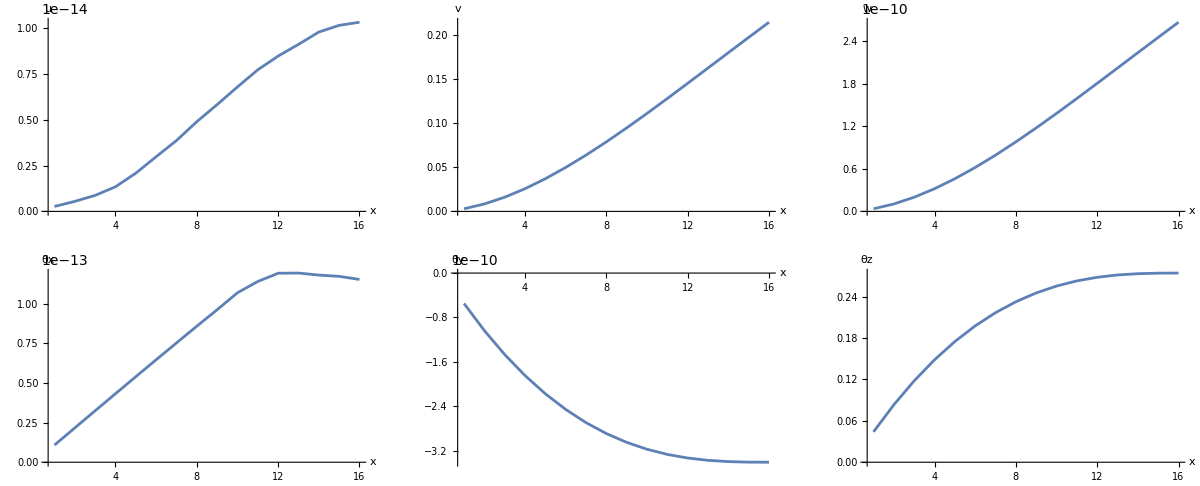
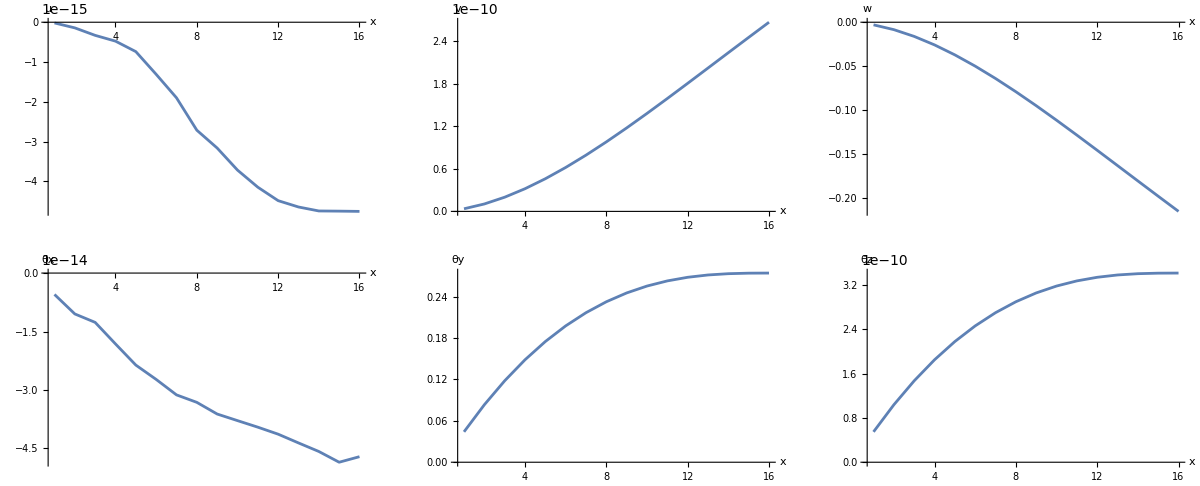
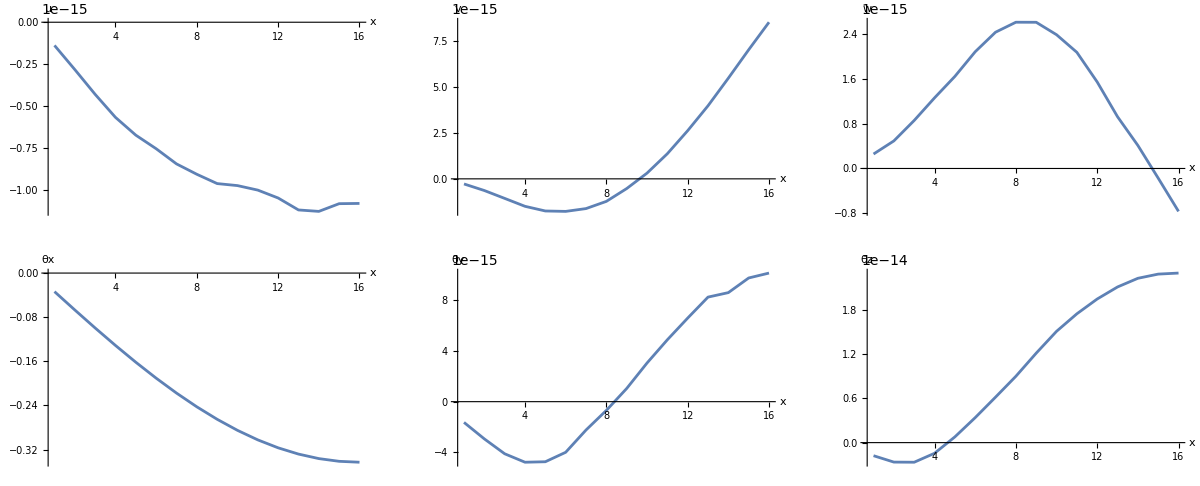
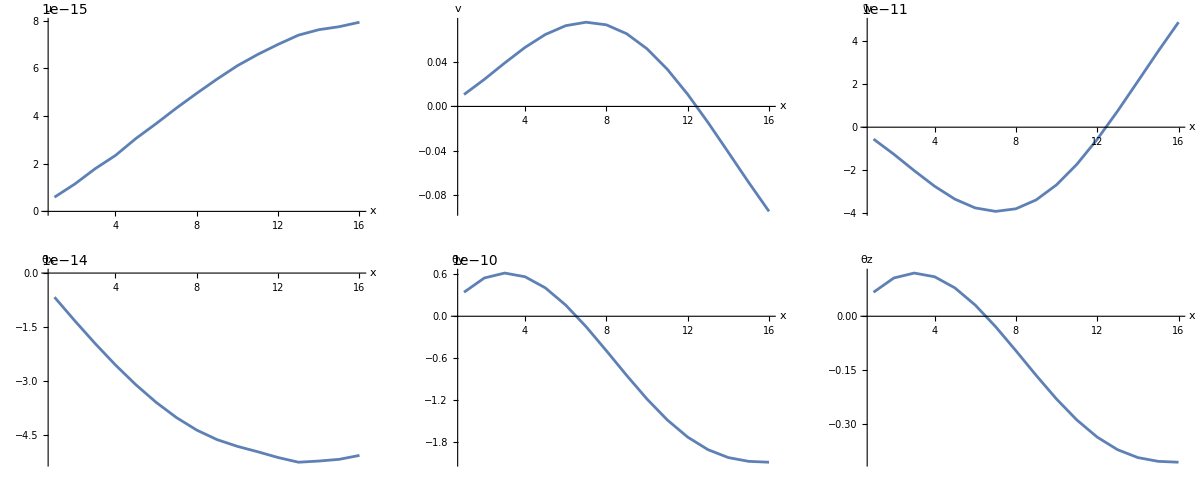
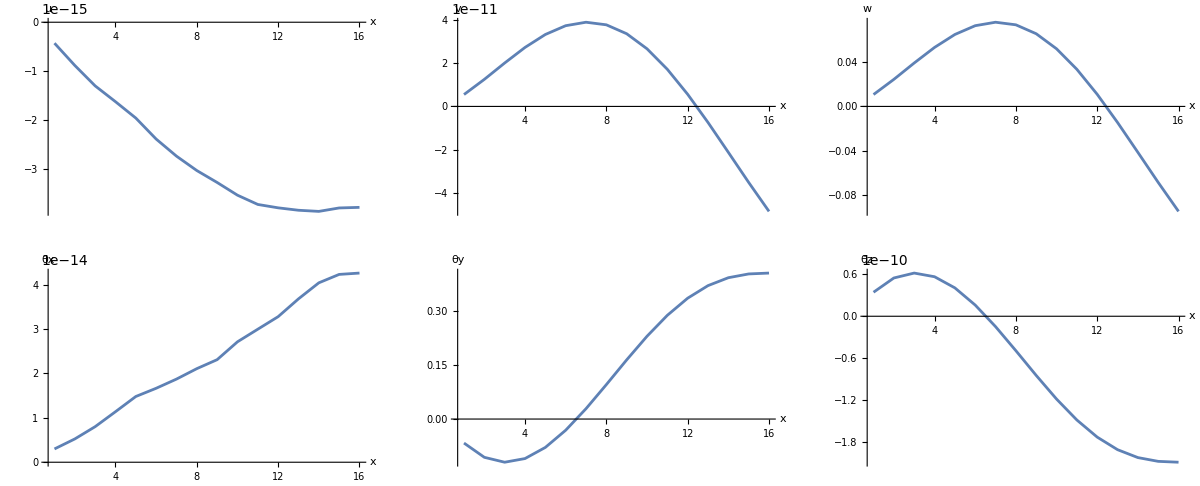
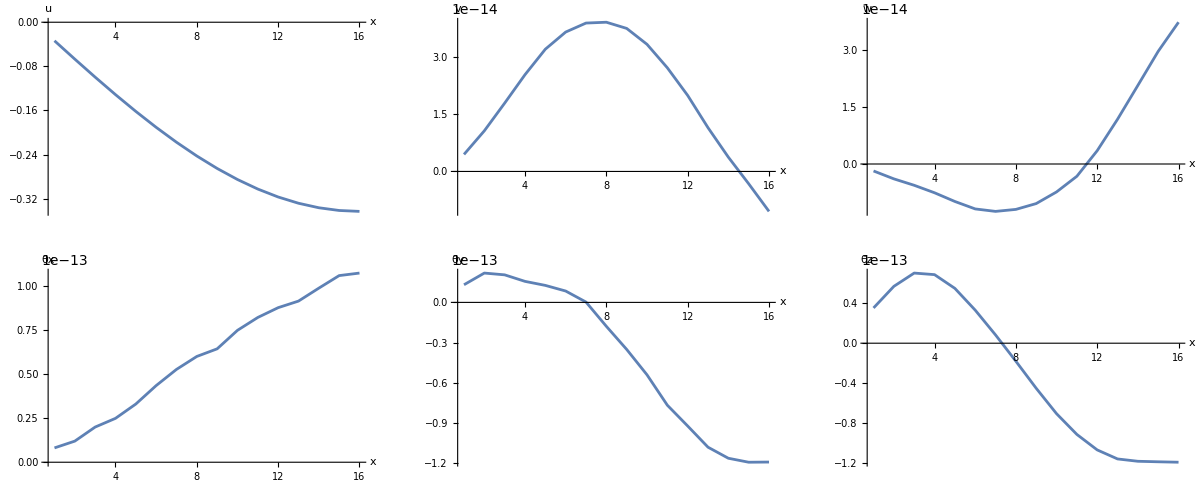
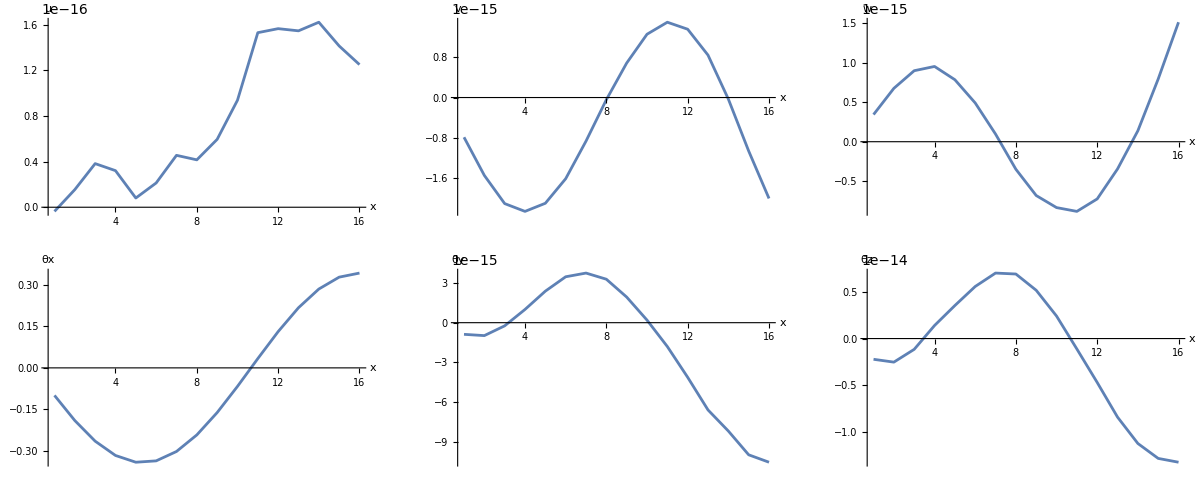
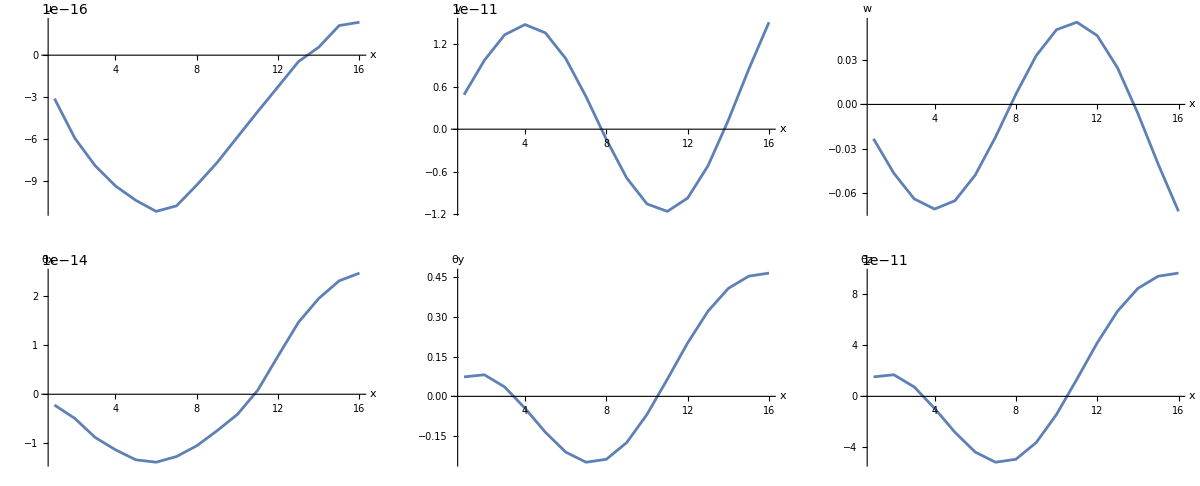
-Graphics-1) modes for freq = 3.9393
-Graphics-2) modes for freq = 3.9393
-Graphics-3) modes for freq = 12.182
-Graphics-4) modes for freq = 16.9589
-Graphics-5) modes for freq = 16.9589
-Graphics-6) modes for freq = 19.6428
-Graphics-7) modes for freq = 36.6634
-Graphics-8) modes for freq = 37.6682
-Graphics-9) modes for freq = 37.6682
-Graphics-10) modes for freq = 59.118
-Graphics-11) modes for freq = 59.843
-Graphics-12) modes for freq = 59.843
-Graphics-13) modes for freq = 61.4984
-Graphics-14) modes for freq = 82.7232

```mathematica
(*display planar mode shape for all 3d modes*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=Sqrt@Reverse[eigs0];
emat1=Reverse[emat];
gg=Table[
title=ToString[ii]<>") modes for freq = "<>ToString[freqs[[ii]]];
emati=Transpose[Partition[emat1[[ii]],6]];
labels=ToString/@{u,v,w,θx,θy,θz};
em1=Sequence/@Thread[{emati,labels}];
g1=GraphicsGrid[Partition[#,3]]&@(Table[ListLinePlot[emati[[i]],PlotRange->All,AxesLabel->{"x",labels[[i]]}],{i,1,6}]);
Panel[ g1,Style[title, "Panel", 16], {{Top, Center}}]
,{ii,1,14}];
Off[ImageDimensions::imginv];
Grid[Transpose[{gg}]]
```

```mathematica
(*************************display of complex modes**********************)
```

```mathematica
(**complex frequencies*)
eigs1=Eigenvalues[mat1];
freqs=Reverse@Chop[eigs1,10^-4];
TableForm[freqs]
```

0.+3.86346 ⅈ
0.-3.86346 ⅈ
0.-3.93623 ⅈ
0.+3.93623 ⅈ
0.-12.1636 ⅈ
0.+12.1636 ⅈ
0.+16.8405 ⅈ
0.-16.8405 ⅈ
0.+16.9909 ⅈ
0.-16.9909 ⅈ
0.-20.1282 ⅈ
0.+20.1282 ⅈ
0.-36.4425 ⅈ
0.+36.4425 ⅈ
0.-37.6238 ⅈ
0.+37.6238 ⅈ
0.-37.8961 ⅈ
0.+37.8961 ⅈ
0.-59.2402 ⅈ
0.+59.2402 ⅈ
0.+59.5697 ⅈ
0.-59.5697 ⅈ
0.-59.8328 ⅈ
0.+59.8328 ⅈ
0.-61.778 ⅈ
0.+61.778 ⅈ
0.-82.5399 ⅈ
0.+82.5399 ⅈ
0.+82.7007 ⅈ
0.-82.7007 ⅈ
0.-87.0983 ⅈ
0.+87.0983 ⅈ
0.+96.3874 ⅈ
0.-96.3874 ⅈ
0.+96.3951 ⅈ
0.-96.3951 ⅈ
0.-99.2344 ⅈ
0.+99.2344 ⅈ
0.-110.122 ⅈ
0.+110.122 ⅈ
0.-110.341 ⅈ
0.+110.341 ⅈ
0.+113.31 ⅈ
0.-113.31 ⅈ
0.-118.738 ⅈ
0.+118.738 ⅈ
0.+118.836 ⅈ
0.-118.836 ⅈ
0.+139.064 ⅈ
0.-139.064 ⅈ
0.-139.445 ⅈ
0.+139.445 ⅈ
0.-140.448 ⅈ
0.+140.448 ⅈ
0.-141.014 ⅈ
0.+141.014 ⅈ
0.+146.615 ⅈ
0.-146.615 ⅈ
0.+146.729 ⅈ
0.-146.729 ⅈ
0.-168.557 ⅈ
0.+168.557 ⅈ
0.+171.507 ⅈ
0.-171.507 ⅈ
0.+172.063 ⅈ
0.-172.063 ⅈ
0.-177.674 ⅈ
0.+177.674 ⅈ
0.-177.743 ⅈ
0.+177.743 ⅈ
0.+182.602 ⅈ
0.-182.602 ⅈ
0.+198.763 ⅈ
0.-198.763 ⅈ
0.+203.673 ⅈ
0.-203.673 ⅈ
0.-204.186 ⅈ
0.+204.186 ⅈ
0.-213.16 ⅈ
0.+213.16 ⅈ
0.+213.218 ⅈ
0.-213.218 ⅈ
0.-226.623 ⅈ
0.+226.623 ⅈ
0.-230.485 ⅈ
0.+230.485 ⅈ
0.+236.462 ⅈ
0.-236.462 ⅈ
0.-236.932 ⅈ
0.+236.932 ⅈ
0.-251.92 ⅈ
0.+251.92 ⅈ
0.+252.097 ⅈ
0.-252.097 ⅈ
0.+263.797 ⅈ
0.-263.797 ⅈ
0.-270.7 ⅈ
0.+270.7 ⅈ
0.+271.101 ⅈ
0.-271.101 ⅈ
0.+272.793 ⅈ
0.-272.793 ⅈ
0.-291.269 ⅈ
0.+291.269 ⅈ
0.-291.803 ⅈ
0.+291.803 ⅈ
0.-298.536 ⅈ
0.+298.536 ⅈ
0.-307.571 ⅈ
0.+307.571 ⅈ
0.-307.71 ⅈ
0.+307.71 ⅈ
0.-321.262 ⅈ
0.+321.262 ⅈ
0.+327.421 ⅈ
0.-327.421 ⅈ
0.-328.317 ⅈ
0.+328.317 ⅈ
0.-333.337 ⅈ
0.+333.337 ⅈ
0.+348.786 ⅈ
0.-348.786 ⅈ
0.-348.804 ⅈ
0.+348.804 ⅈ
0.-358.961 ⅈ
0.+358.961 ⅈ
0.+359.497 ⅈ
0.-359.497 ⅈ
0.-365.845 ⅈ
0.+365.845 ⅈ
0.-372.261 ⅈ
0.+372.261 ⅈ
0.+381.036 ⅈ
0.-381.036 ⅈ
0.-381.171 ⅈ
0.+381.171 ⅈ
0.+390.494 ⅈ
0.-390.494 ⅈ
0.-390.511 ⅈ
0.+390.511 ⅈ
0.-394.363 ⅈ
0.+394.363 ⅈ
0.+400.856 ⅈ
0.-400.856 ⅈ
0.-400.91 ⅈ
0.+400.91 ⅈ
0.-416.215 ⅈ
0.+416.215 ⅈ
0.-425.616 ⅈ
0.+425.616 ⅈ
0.+428.123 ⅈ
0.-428.123 ⅈ
0.+447.758 ⅈ
0.-447.758 ⅈ
0.+447.765 ⅈ
0.-447.765 ⅈ
0.-480.67 ⅈ
0.+480.67 ⅈ
0.-498.115 ⅈ
0.+498.115 ⅈ
0.-498.118 ⅈ
0.+498.118 ⅈ
0.-535.969 ⅈ
0.+535.969 ⅈ
0.+547.474 ⅈ
0.-547.474 ⅈ
0.-547.475 ⅈ
0.+547.475 ⅈ
0.-588.92 ⅈ
0.+588.92 ⅈ
0.+592.87 ⅈ
0.-592.87 ⅈ
0.-592.871 ⅈ
0.+592.871 ⅈ
0.-630.944 ⅈ
0.+630.944 ⅈ
0.-630.947 ⅈ
0.+630.947 ⅈ
0.+635.599 ⅈ
0.-635.599 ⅈ
0.-658.425 ⅈ
0.+658.425 ⅈ
0.-658.431 ⅈ
0.+658.431 ⅈ
0.-671.044 ⅈ
0.+671.044 ⅈ
0.-673.309 ⅈ
0.+673.309 ⅈ
0.-673.317 ⅈ
0.+673.317 ⅈ
0.-690.343 ⅈ
0.+690.343 ⅈ

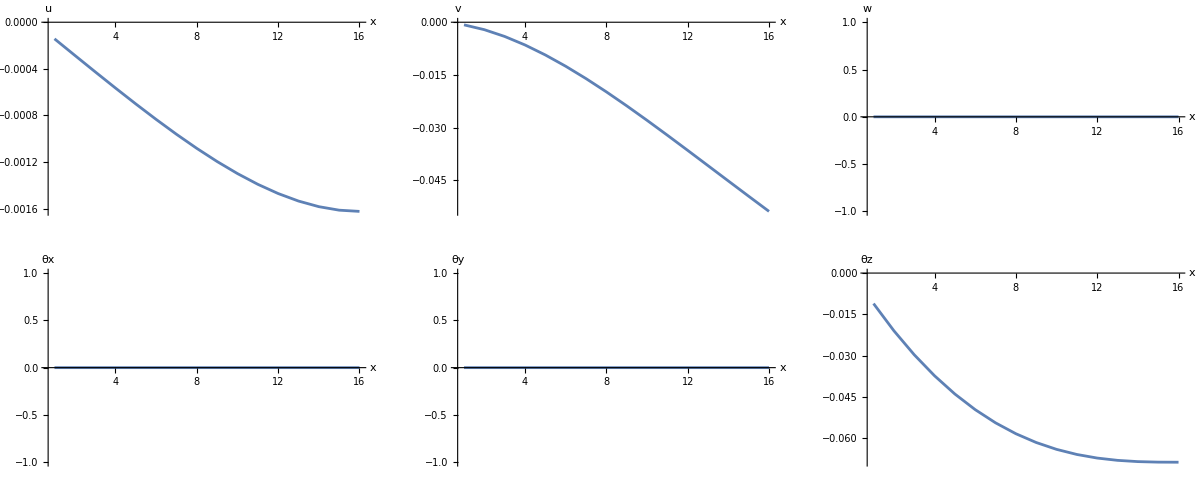
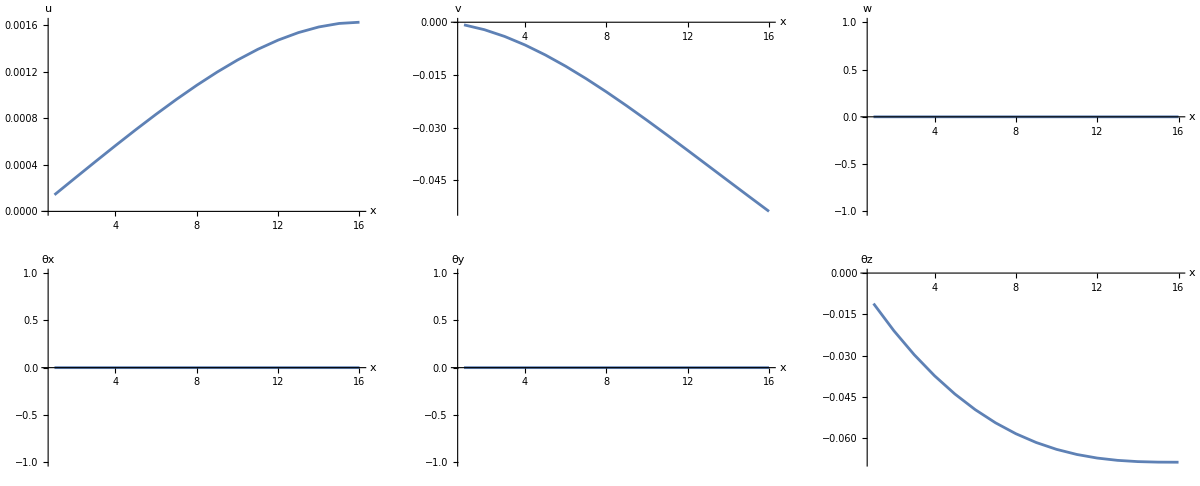
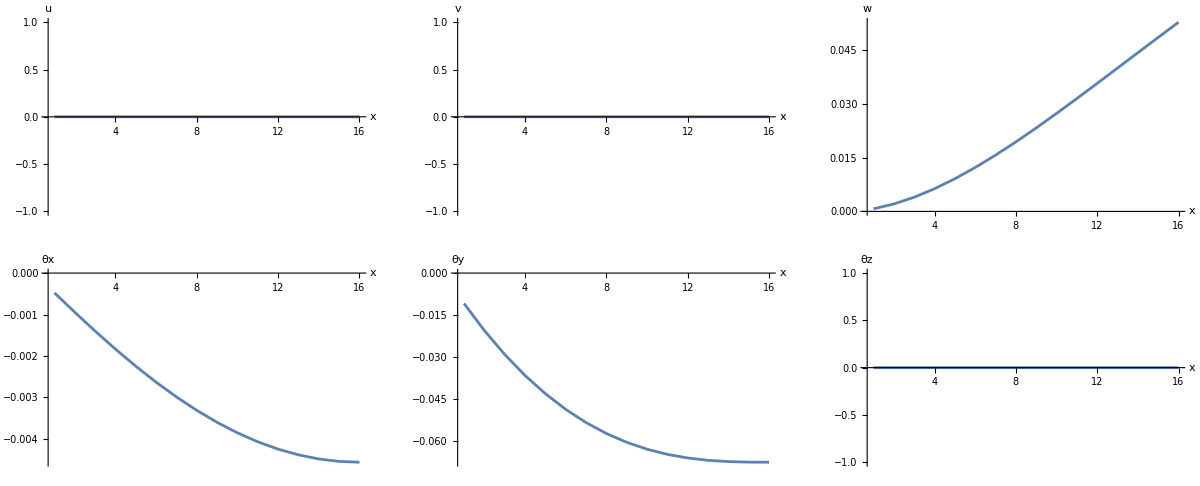
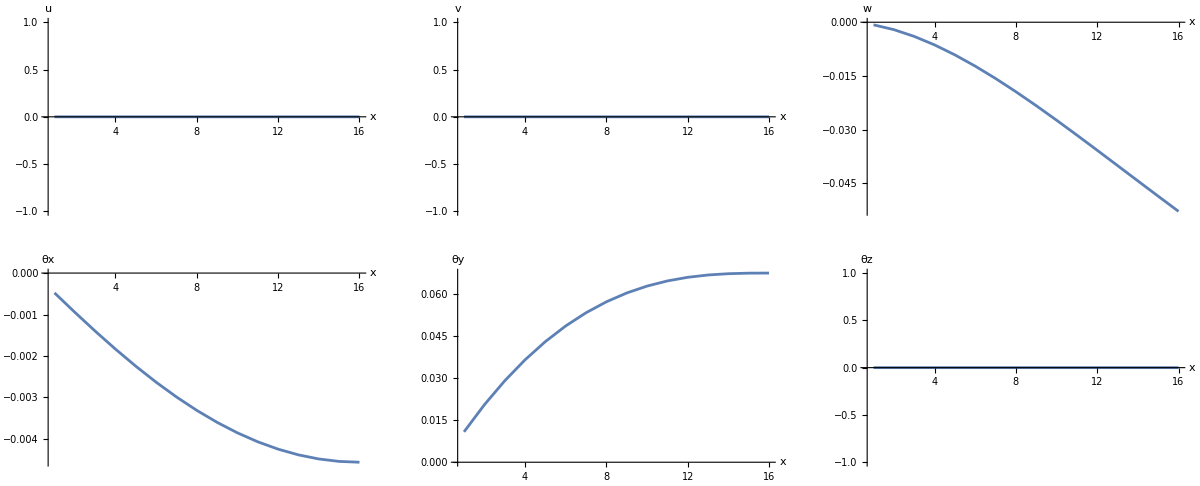
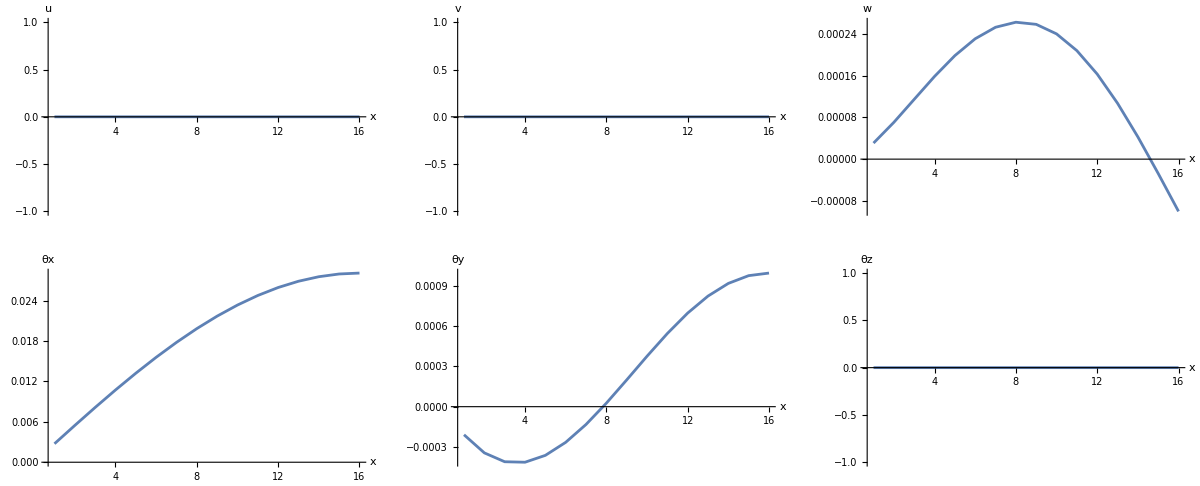
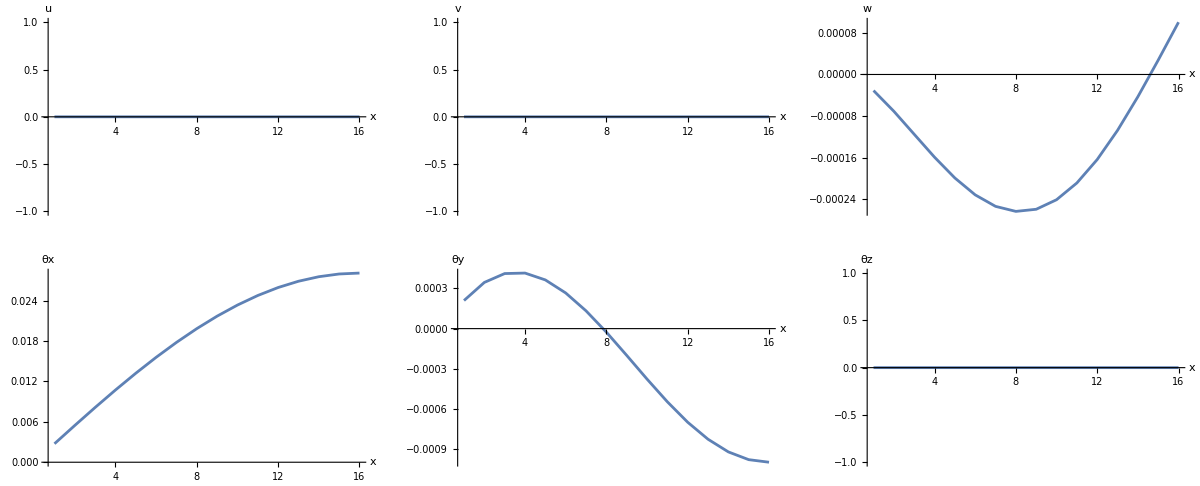
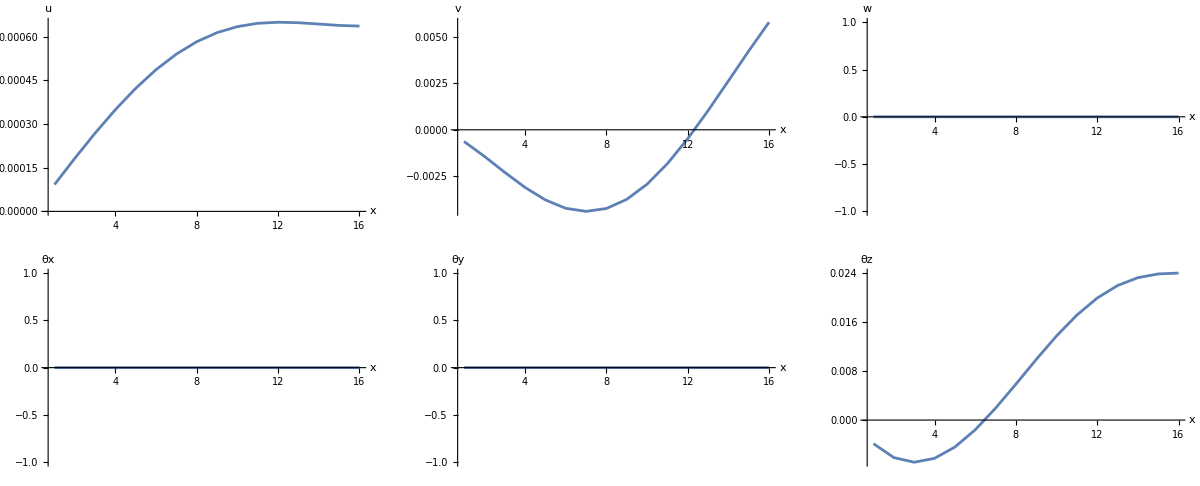
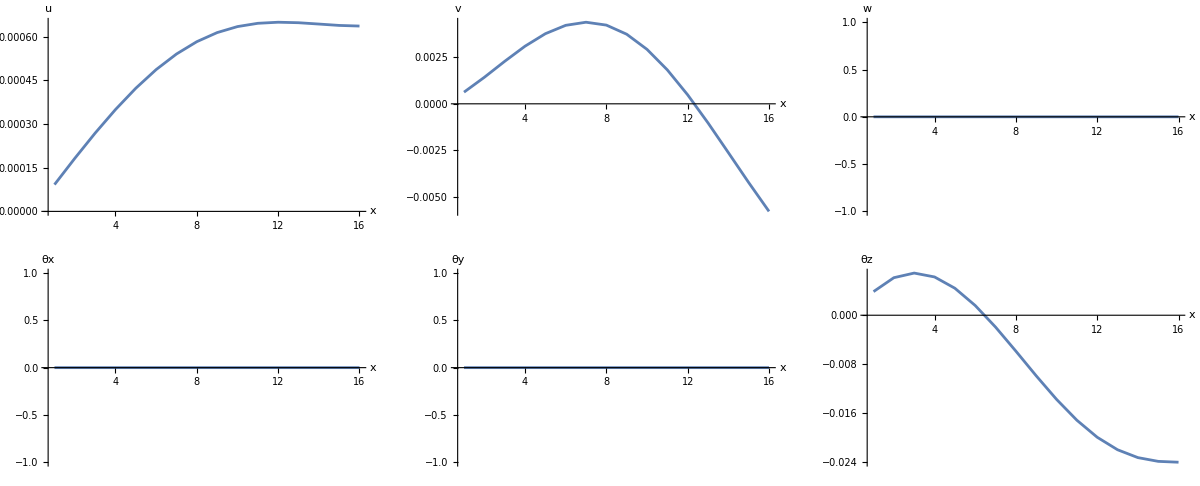
-Graphics-1) modes for freq = 0. + 3.86346 I
-Graphics-2) modes for freq = 0. - 3.86346 I
-Graphics-3) modes for freq = 0. - 3.93623 I
-Graphics-4) modes for freq = 0. + 3.93623 I
-Graphics-5) modes for freq = 0. - 12.1636 I
-Graphics-6) modes for freq = 0. + 12.1636 I
-Graphics-7) modes for freq = 0. + 16.8405 I
-Graphics-8) modes for freq = 0. - 16.8405 I
-Graphics-9) modes for freq = 0. + 16.9909 I
-Graphics-10) modes for freq = 0. - 16.9909 I
-Graphics-11) modes for freq = 0. - 20.1282 I
-Graphics-12) modes for freq = 0. + 20.1282 I
-Graphics-13) modes for freq = 0. - 36.4425 I
-Graphics-14) modes for freq = 0. + 36.4425 I
-Graphics-15) modes for freq = 0. - 37.6238 I
-Graphics-16) modes for freq = 0. + 37.6238 I
-Graphics-17) modes for freq = 0. - 37.8961 I
-Graphics-18) modes for freq = 0. + 37.8961 I
-Graphics-19) modes for freq = 0. - 59.2402 I
-Graphics-20) modes for freq = 0. + 59.2402 I

```mathematica
(*display of mode shapes*)

eps=10^-5;

nmodes=20;

nelems=16;

{eigs0,emat}=Chop[Eigensystem[mat1],eps];

freqs=Reverse[Chop[eigs0,eps]];

emat1=Reverse[emat];

gg=Table[

title=ToString[ii]<>") modes for freq = "<>ToString[freqs[[ii]]];

ab[a_]:=Module[{ans},If[Im[a]!=0,ans=I*a,ans=a];Return[ans]];

SetAttributes[ab,Listable];

emati=Transpose[Partition[Take[ab@emat1[[ii]],-16*6],6]];

labels=ToString/@{u,v,w,θx,θy,θz};

em1=Sequence/@Thread[{emati,labels}];

g1=GraphicsGrid[Partition[#,3]]&@(Table[ListLinePlot[emati[[i]],PlotRange->All,AxesLabel->{"x",labels[[i]]}],{i,1,6}]);

Panel[ g1,Style[title, "Panel", 16], {{Top, Center}}]

,{ii,1,nmodes}];

Off[ImageDimensions::imginv];

Grid[Transpose[{gg}]]
```

```mathematica
(**display table of values of different variables in the mode shape*)
modeno=1;
modei=Chop@ab@(Partition[Take[#,-Length[#]/2],6])&@emat1[[modeno]];
ch=ToString/@{u,v,w,θx,θy,θz};
rh=ToString/@Table[i,{i,1,nelems}];
TableForm[modei,TableHeadings->{rh,ch}]
```

| u | v | w | θx | θy | θz
1 | -0.000142449 | -0.000745639 | 0 | 0 | 0 | -0.0110762
2 | -0.000284536 | -0.00211987 | 0 | 0 | 0 | -0.0209346
3 | -0.000425682 | -0.0040509 | 0 | 0 | 0 | -0.0296487
4 | -0.000565089 | -0.00647098 | 0 | 0 | 0 | -0.0372868
5 | -0.000701772 | -0.00931605 | 0 | 0 | 0 | -0.043913
6 | -0.000834583 | -0.0125255 | 0 | 0 | 0 | -0.0495887
7 | -0.000962235 | -0.0160421 | 0 | 0 | 0 | -0.0543744
8 | -0.00108332 | -0.0198119 | 0 | 0 | 0 | -0.0583305
9 | -0.00119635 | -0.0237843 | 0 | 0 | 0 | -0.0615193
10 | -0.00129973 | -0.0279121 | 0 | 0 | 0 | -0.0640066
11 | -0.00139184 | -0.032152 | 0 | 0 | 0 | -0.0658628
12 | -0.00147102 | -0.0364647 | 0 | 0 | 0 | -0.067165
13 | -0.00153555 | -0.0408156 | 0 | 0 | 0 | -0.0679981
14 | -0.00158375 | -0.0451751 | 0 | 0 | 0 | -0.0684564
15 | -0.0016139 | -0.0495195 | 0 | 0 | 0 | -0.0686446
16 | -0.00162432 | -0.0538319 | 0 | 0 | 0 | -0.0686794

```mathematica
(****new tables**)

(*table 1*)

Off[Solve::svars];

AbsoluteTiming@With[

{L1=1,ay1=0.08,az1=0.08,νy=0,νz=0,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,

ky=0.85,kz=0.85,nelems=16,η=0,TheoryType="Euler",btype="CF"},

gp={ay->0.08,az->0.08,L->L1}; 

Print[{nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType}]; 

mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType]; ]//Print;

om0=(Sqrt[Ei/ro]*ay/L1)/.gp/.{Ei->190*10^9,ro->7830};

om0=1; (*dimensionaless*)

(**planar form*)

{eigs0,emat}=Eigensystem[{Kstar,Meeg}];

freqs=FilterF[{eigs0,emat}];

TableForm[Thread[{Table[i,{i,1,Length[#]}],#}]&@(freqs//Take[#,10]&),TableHeadings -> {{}, {"mode","frequency"}}]
```

{16,0.3,{0.85,0.85},0,0,{0,0},0,{ay→0.08,az→0.08,L→1},1,0,CF,Euler}

{{ξ},{ξ},{ξ},{ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{9.71297,Null}

| mode | frequency
 | 1 | 3.51602
 | 2 | 22.0346
 | 3 | 61.6997
 | 4 | 120.92
 | 5 | 199.941
 | 6 | 298.824
 | 7 | 417.709
 | 8 | 556.828
 | 9 | 716.524
 | 10 | 897.274

```mathematica
(*Table 2 (mode vs taper ratio) Note: taper ratio can be different in vz and vy *)
νs={{0.1,0.1},{0.2,0.4}};
AbsoluteTiming@With[
{L1=0.72,ay1=0.08,az1=0.08,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,
ky=0.85,kz=0.85,nelems=16,η=0,TheoryType="Timo",btype="CF"},
gp={ay->ay1,az->az1,L->L1}; 
freqG={};
Table[
Print@nu;
{νy,νz}=nu;
mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType];
om0=1; (*dimensionaless*)
(**planar form*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=FilterF[{eigs0,emat}];
AppendTo[freqG,freqs];
,{nu,νs}]
]//Print;
nmodes=5;
cheadings=Table[("νy = "<>#[[1]]<>"\n"<>"νz = "<>#[[2]])&@(ToString/@νs[[i]]),{i,1,Length[νs]}];
TableForm[Transpose@(Take[#,nmodes]&/@freqG),TableHeadings -> {ToString/@Table[i,{i,1,nmodes}],cheadings}]
```

{0.1,0.1}

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{0.2,0.4}

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{103.846,{Null,Null}}

| νy = 0.1
νz = 0.1 | νy = 0.2
νz = 0.4
1 | 3.47626 | 3.79028
2 | 16.286 | 15.6986
3 | 36.3714 | 34.1904
4 | 58.3153 | 55.4669
5 | 81.4717 | 78.6158

```mathematica
(*Table 3 dimensionless speed vs frequency (filtered frequency)*)
etas={0,1,2,3};
AbsoluteTiming@With[
{L1=0.72,ay1=0.08,az1=0.08,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,νy=0.1,νz=0.2,
ky=0.85,kz=0.85,nelems=16,TheoryType="Timo",btype="CF"},
gp={ay->ay1,az->az1,L->L1}; 
freqG={};
Table[
Print@η;
mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType];
om0=1; (*dimensionaless*)
(**planar form*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=FilterF[{eigs0,emat}];
AppendTo[freqG,freqs];
,{η,etas}]
]//Print;
nmodes=5;
cheadings=Table[ToString@eta,{eta,etas}];
rheadings=ToString/@Table[i,{i,1,nmodes}];
TableForm[Take[#,nmodes]&/@freqG,TableHeadings->{cheadings,rheadings}]
```

0

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

1

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

2

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

3

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{226.598,{Null,Null,Null,Null}}

| 1 | 2 | 3 | 4 | 5
0 | 3.53047 | 16.066 | 35.6842 | 57.5086 | 80.8245
1 | 3.66662 | 16.2058 | 35.8562 | 57.7231 | 81.0782
2 | 4.04596 | 16.6178 | 36.3658 | 58.3593 | 81.8308
3 | 4.60479 | 17.2815 | 37.1949 | 59.3964 | 83.057

```mathematica
(**Table 4 frequency vs gyration ratio (filtered frequency)***)
as={0.1,0.2,0.3};
AbsoluteTiming@With[
{L1=0.72,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,νy=0.1,νz=0.2,η=0.1,
ky=0.85,kz=0.85,nelems=16,TheoryType="Timo",btype="CF"},
freqG={};
Table[
Print@a;
gp={ay->a,az->a,L->L1};
mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType];
om0=1; (*dimensionaless*)
(**planar form*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=FilterF[{eigs0,emat}];
AppendTo[freqG,freqs];
,{a,as}]
]//Print;
nmodes=5;
cheadings=Table[ToString@a,{a,as}];
rheadings=ToString/@Table[i,{i,1,nmodes}];
TableForm[Transpose@(Take[#,nmodes]&/@freqG),TableHeadings->{rheadings,cheadings}]
```

0.1

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

0.2

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

0.3

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{174.467,{Null,Null,Null}}

| 0.1 | 0.2 | 0.3
1 | 3.43718 | 2.87987 | 2.37137
2 | 14.5124 | 9.05271 | 6.28207
3 | 31.1101 | 17.9519 | 10.9937
4 | 48.6066 | 21.1397 | 13.6968
5 | 66.691 | 28.9536 | 18.4248

```mathematica
(*Table 5 slenderness ratio (L/rgy) vs filtered frequency*)
slr={1,10,100};
AbsoluteTiming@With[
{L1=0.72,ψ=0 Degree,ϕ=0 Degree,μ=0.3,R0=0,νy=0.1,νz=0.2,η=0.1,
ky=0.85,kz=0.85,nelems=16,TheoryType="Timo",btype="CF"},
freqG={};
Table[
Print@sl;
gp={ay->1/sl,az->1/sl,L->L1};
mat1=Assemble[nelems,μ,{ky,kz},νy,νz,{ψ,ϕ},η,gp,L1,R0,btype,TheoryType];
om0=1; (*dimensionaless*)
(**planar form*)
{eigs0,emat}=Eigensystem[{Kstar,Meeg}];
freqs=FilterF[{eigs0,emat}];
AppendTo[freqG,freqs];
,{sl,slr}]
]//Print;
nmodes=1;
cheadings=Table[ToString@sl,{sl,slr}];
rheadings=ToString/@Table[i,{i,1,nmodes}];
TableForm[Thread[{slr,(Take[#,nmodes]&/@freqG)}],TableHeadings->{{},{"L/rgy","frequency"}}]
```

1

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

10

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

100

{{i,ξ},{i,ξ},{i,ξ},{i,ξ},{i,ξ}}

Generating bcs

integrating elemental matrices

assembling elemntal matrices

{167.049,{Null,Null,Null}}

| L/rgy | frequency
 | 1 | 0.927765
 | 10 | 3.43718
 | 100 | 43.9583